# DSolve examples

Katharine Long, Texas Tech University

### Some first order equations

#### Solve y'=-3y

Write the equation y'=-3y in the form y’[t]==-3y[t]. Note the double equal sign “==” is used in writing an equation (this distinguishes it from the use of “=” to mean assignment). 

Along with the equation, we also need to tell DSolve what is our unknown (in this case, y[t]) and our independent variable (in this case, t). Here’s how it’s done:

```mathematica
DSolve[y'[t]==-3 y[t],y[t],t]
```

{{y(t)→1 ⅇ^(-3 t)}}

The solution is c_1 e^(-3t), where c_1 is an undetermined constant.

#### Solve y'=-3y with initial conditions

To include initial conditions, form a list (using curly braces) that includes the equation and the initial condition. If we have y'=-3y with initial conditions y(0)=2, we write {y’[t]==-3y[t], y[0]==2}, again using double equal signs.

```mathematica
DSolve[{y'[t]==-3 y[t],y[0]==2},y[t],t]
```

{{y(t)→2 ⅇ^(-3 t)}}

#### What to do with the result of DSolve

You’ll have noticed that DSolve returns something like  {{y(t)→2 ⅇ^(-3 t)}} instead of a function. In Mathematica, an expression such as a→ b is a replacement rule which, when applied, replaces the expression a by the expression b. A rule is applied using the “/.” (pronounced “slash-dot”) operator. For a trivial example, let’s apply the rule a→ b to the expression a^2+1

```mathematica
(a^2 + 1) /. a->b
```

b^2+1

Here’s an example that occurs in integration by trig substitution:

```mathematica
Sqrt[1-x^2] /. x->Sin[x]/. 1-Sin[x]^2 ->Cos[x]^2
```

√(cos^2(x))

Now that we’ve seen how to use rules, let’s run DSolve and assign the result to a variable “solnRule”

```mathematica
solnRule=DSolve[{y'[t]==-3 y[t],y[0]==2},y[t],t]
```

{{y(t)→2 ⅇ^(-3 t)}}

This is a rule that can replace y[t] by 2 e^(-3t). There are two sets of curly braces: the inner set is because we might have multiple unknowns (see below for an example of that in a coupled system), the outer set is because we might have multiple solutions. With only one solution, we only need the first solution rule solnRule[[1]]. 

Let’s construct a function for our solution. We apply the first solution rule to the expression y[t], which substitutes 2 e^(-3t) for y(t)

```mathematica
ySoln[t_]=y[t] /.solnRule[[1]]
```

2 ⅇ^(-3 t)

Now we can use this as an ordinary function: we can plot it, integrate it, whatever you’d want to do with a function.

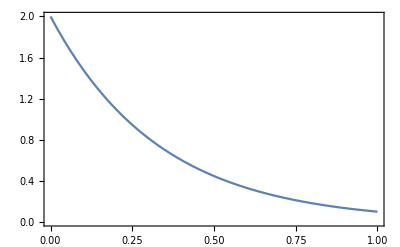

```mathematica
Plot[ySoln[t],{t,0,1}]
```

#### Another separable example

```mathematica
DSolve[{y'[t]==Exp[t](1+y[t]^2),y[0]==0},y[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y(t)→-tan(1-ⅇ^t)}}

#### A Bernoulli equation

“Bernoulli equations” are equations of the form y'=p(t)y+q(t)y^n, n≠ 1, and can be transformed to first order linear equations by a change of variables. Here’s a simple Bernoulli equation

```mathematica
DSolve[y'[t]==-2y[t]+t y[t]^4,y[t],t]
```

{{y(t)→-(-3^(1/3) 2^(2/3))/((6 t+12 1 ⅇ^(6 t)+1)^(1/3))},{y(t)→((-2)^(2/3) 3^(1/3))/((6 t+12 1 ⅇ^(6 t)+1)^(1/3))},{y(t)→(2^(2/3) 3^(1/3))/((6 t+12 1 ⅇ^(6 t)+1)^(1/3))}}

There are three solutions because inverting the transformation in this case involves taking a cube root.

#### The logistic equation

This equation is important in population biology and chemical kinetics. It is a Bernoulli equation, but can also be solved by separation of variables.

```mathematica
DSolve[y'[t]==y[t]-y[t]^2,y[t],t]
```

{{y(t)→ⅇ^t/(ⅇ^t+ⅇ^1)}}

#### An equation from mechanics

```mathematica
DSolve[y'[t]==Sqrt[1-y[t]^2],y[t],t]
```

{{y(t)→sin(t+1)}}

#### An equation with no known closed-form solution

Not all differential equations can be solved in closed form. If DSolve doesn’t know how to solve an equation, it just prints out “DSolve” with the arguments you gave it .

```mathematica
DSolve[{y'[t]==t y[t]^2+y[t]^4,y[0]==0},y[t],t]
```

DSolve[{y'(t)==(y(t))^4+t (y(t))^2,y(0)==0},y(t),t]

### A common error and how to fix it

Probably the most common mistake when using DSolve is to use a single equal sign instead of the double equal. Here’s what happens

```mathematica
DSolve[y'[t]=-3y[t],y[t],t]
```

DSolve::deqn: Equation or list of equations expected instead of -3 y(t) in the first argument -3 y(t).

DSolve[-3 y(t),y(t),t]

Doh! Easy enough to fix; just use the double equal sign...

```mathematica
DSolve[y'[t]==-3y[t],y[t],t]
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument True.

DSolve[True,y(t),t]

Unfortunately that didn’t work; it’s because when you used the single equal sign you set y’[t] to -3y[t], and so then the equality test y’[t]==-3y[t]  returns “True”. You need to tell Mathematica to forget your accidental assignment to y[t], which you do with

```mathematica
Remove[y]
```

```mathematica
DSolve[y'[t]==-3y[t],y[t],t]
```

{{y(t)→1 ⅇ^(-3 t)}}

All good again!

### Some second order equations

#### An underdamped oscillator

Here’s an underdamped oscillator. The general solution now has two undetermined coefficients

```mathematica
DSolve[y''[t]+2y'[t]+10y[t]==0,y[t],t]
```

{{y(t)→2 ⅇ^-t cos(3 t)+1 ⅇ^-t sin(3 t)}}

To determine the constants, we need two initial conditions. Just put the initial conditions in a list (using curly braces) as we did with a first order equation.

```mathematica
solnRule=DSolve[{y''[t]+2y'[t]+10y[t]==0,y[0]==1,y'[0]==0},y[t],t]
```

{{y(t)→1/3 ⅇ^-t (sin(3 t)+3 cos(3 t))}}

Let’s plot the solution and its derivative

```mathematica
ySoln[t_]=y[t]/. solnRule[[1]]
```

1/3 ⅇ^-t (sin(3 t)+3 cos(3 t))

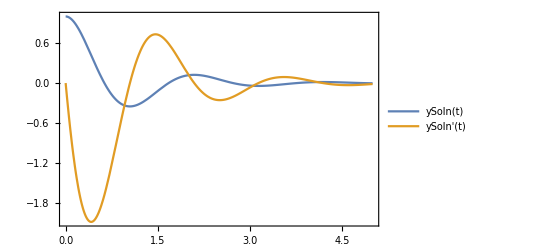

```mathematica
Plot[{ySoln[t],ySoln'[t]},{t,0,5},PlotRange->All,PlotLegends->"Expressions"]
```

#### A critically damped oscillator

```mathematica
DSolve[y''[t]+6y'[t]+9y[t]==0,y[t],t]
```

{{y(t)→1 ⅇ^(-3 t)+2 ⅇ^(-3 t) t}}

#### Forced harmonic oscillators

Here’s an oscillator forced by f(t)=1+t

```mathematica
DSolve[y''[t]+2y'[t]+10y[t]==t+1,y[t],t]//FullSimplify
```

{{y(t)→1/50 (5 t+4)+ⅇ^-t (2 cos(3 t)+1 sin(3 t))}}

You could have done that one easily by hand. However, solutions to forced oscillator can quickly get complicated. Luckily the computer has more patience than you or I and will happily solve problems such as an oscillator forced by t^5 e^(-3t)cos(4t)

```mathematica
DSolve[y''[t]+2y'[t]+10y[t]==t^5Exp[-3t]Cos[4t],y[t],t]//FullSimplify
```

{{y(t)→1/69263628528125 ⅇ^(-3 t) (-8 (265 t (265 t (265 t (265 t (106 t+199)+27792)-14002248)-7977154992)-1296730086984) sin(4 t)-(265 t (265 t (265 t (265 t (159 t+1756)+1113348)+381893088)+68538473352)+3891668308704) cos(4 t)+69263628528125 ⅇ^(2 t) (2 cos(3 t)+1 sin(3 t)))}}

I don’t know about you, but I’d not want to do that by hand.

#### Linear equations with non-constant coefficients

So far, you’ve learned how to solve linear second order equations with constant coefficients. We’ll soon move on to equations with variable coefficients. As an initial example, let’s solve x^2 u''+2x u'+u =0.

```mathematica
DSolve[x^2 u''[x]+2x u'[x]+u[x]==0,u[x],x]
```

{{u(x)→(2 cos(1/2 √3 log(x)))/(√x)+(1 sin(1/2 √3 log(x)))/(√x)}}

The solution involves familiar elementary functions. In our next example, we’ll see some functions that might not be familiar.

```mathematica
DSolve[x^2 u''[x]+x u'[x]+x^2u[x]==0,u[x],x]
```

{{u(x)→1 0x+2 0x}}

If you don’t know what J_0(x) and Y_0(x) are then you can run the mouse over the output line to see that they are Bessel functions. We’ll be seeing a lot more of Bessel functions later.

#### A nonlinear second order equation

The pendulum equation is y''+sin(y)=0, which is nonlinear. We used a small angle approximation to get the harmonic oscillator equation y''+y=0, but in cases where the angle isn’t small we need to use the full nonlinear equation.

```mathematica
DSolve[{y''[t]+Sin[y[t]]==0,y[0]==1,y'[0]==0},y[t],t]
```

{{y(t)→2 1/2 (2 1/2csc^2(1/2)-t √(2 (1-cos(1))))csc^2(1/2)}}

This solution involves unfamiliar functions “am” and “F”. Run your mouse over them and consult Mathematica’s help to find out what they are (they’re a Jacobi elliptic function and an elliptic integral).

#### A nonlinear equation with no known closed-form solution

Add a forcing term to the pendulum equation, and the problem no longer has a closed form solution

```mathematica
DSolve[{y''[t]+Sin[y[t]]==Cos[t],y[0]==1,y'[0]==0},y[t],t]
```

DSolve[{y''(t)+sin(y(t))==cos(t),y(0)==1,y'(0)==0},y(t),t]

### Solving systems of equations

DSolve can handle systems of coupled differential equations. Here’s how to solve

x''=-2x+y
y''=x - 2y

```mathematica
DSolve[{
x''[t]==-2x[t]+y[t], 
y''[t]==x[t]-2y[t],
x[0]==1,x'[0]==0,
y[0]==0,y'[0]==2
},{x[t],y[t]},t]
```

{{x(t)→1/6 (6 sin(t)-2 √3 sin(√3 t)+3 cos(t)+3 cos(√3 t)),y(t)→1/6 (6 sin(t)+2 √3 sin(√3 t)+3 cos(t)-3 cos(√3 t))}}

You should try solving this using eigenvalue methods (it’s not hard)